```mathematica
Clear[allGraphs]
```

```mathematica
colors=2;
```

```mathematica
allGraphs=allGraphs4;
```

```mathematica
allKey=K4Key;
```

```mathematica
SymbolToLabel2[s_]:=Block[{blocks=StringSplit[StringDrop[SymbolName[s ],1],"x"]},
blocks=Select[blocks,StringLength[#]>1&];
If[Length[blocks]==0,
Style[OverHat[1],Darker[Darker[Red]],12]
,
If[StringLength[blocks[[1]]]==nodeCount,
Style[OverHat[0],Darker[Darker[Red]],12]
,
Row[Riffle[blocks ,Style["♁",Darker[Darker[Green]],12]]]
]
]
]
```

```mathematica
fullAtoms=Sort[allGraphs4AtomKeys,CompareSymbols[allGraphs[#1,"colofour"],allGraphs[#2,"colofour"]]&];
```

```mathematica
nullAtoms=Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs[#1,"colofourrealnull"],allGraphs[#2,"colofourrealnull"]]&];
```

```mathematica
CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2,p1,p2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
p1=StringToPartition[str1];
p2=StringToPartition[str2];
c1=PartitionFaculty[p1];
c2=PartitionFaculty[p2];
If[c1≠c2,
Less[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
fullSymbols=Sort[Table[allGraphs[k,"colofour"],{k,fullAtoms}],CompareSymbols];
```

```mathematica
nullSymbols=Sort[Table[allGraphs[k,"colofourrealnull"],{k,nullAtoms}],CompareSymbols];
```

```mathematica
fullVars=Table[Indexed[f,SymbolToLabel2[s]],{s,fullSymbols}];
```

```mathematica
nullVars=Table[Indexed[n,SymbolToLabel2[s]],{s,nullSymbols}];
```

## Start computations

```mathematica
mobius=MobiusMatrix[allGraphs];
```

```mathematica
zeta=Inverse[mobius];
```

```mathematica
NullVector[k_]:=Table[Coefficient[allGraphs[k,"colofourrealnull"],s],{s,nullSymbols }]
```

```mathematica
FullVector[k_]:=Table[Coefficient[allGraphs[k,"colofour"],s],{s,fullSymbols}]
```

```mathematica
Table[NullVector[k],{k,fullAtoms}]//MatrixForm
```

(1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | -6
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 2
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 2
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(*Table[k->NullVector[k].zeta==FullVector[k],{k,Keys[allGraphs]}]*)
```

## Now do some solving

```mathematica
nodeCount=VertexCount[allGraphs[0,"graph"]]
```

4

```mathematica
tailLength=Sum[StirlingS2[nodeCount,k],{k,1,colors}]
```

8

```mathematica
vectorLength=BellB[nodeCount]
```

15

```mathematica
Column[{"^","1"},Spacings->{0,0}]
```

^
1

```mathematica
Table[SymbolToLabel2[ s],{s,fullSymbols}]
```

{OverHat[1],34,23,24,12,13,14,12♁34,13♁24,14♁23,234,123,124,134,OverHat[0]}

```mathematica
Table[Indexed[f,SymbolToLabel2[ k]],{k,fullSymbols}];
```

```mathematica
fullPositive=Table[Indexed[f,SymbolToLabel2[ k]],{k,Take[fullSymbols,vectorLength-tailLength]}]
```

{fOverHat[1],f34,f23,f24,f12,f13,f14}

```mathematica
fullZero=Table[Indexed[f,SymbolToLabel2[ k]],{k,Take[fullSymbols,-tailLength]}]
```

{f12♁34,f13♁24,f14♁23,f234,f123,f124,f134,fOverHat[0]}

```mathematica
fullVec=Join[fullPositive,Table[0,{k,1,tailLength}]]
```

{fOverHat[1],f34,f23,f24,f12,f13,f14,0,0,0,0,0,0,0,0}

```mathematica
fullVec2=Table[Indexed[f,SymbolToLabel2[ k]],{k,Take[fullSymbols,vectorLength]}]
```

{fOverHat[1],f34,f23,f24,f12,f13,f14,f12♁34,f13♁24,f14♁23,f234,f123,f124,f134,fOverHat[0]}

```mathematica
nullPositive=Table[Indexed[n,SymbolToLabel2[ k]],{k,Take[fullSymbols,vectorLength-tailLength]}]
```

{nOverHat[1],n34,n23,n24,n12,n13,n14}

```mathematica
nullZero=Table[Indexed[n,SymbolToLabel2[ k]],{k,Take[fullSymbols,-tailLength]}]
```

{n12♁34,n13♁24,n14♁23,n234,n123,n124,n134,nOverHat[0]}

```mathematica
k6VecRep=Table[nullSymbols[[k]]->Sign[NullVector[K6Key][[k]]],{k,vectorLength}]
```

{n1x2x3x4→0,n1x2x34→0,n1x23x4→0,n1x24x3→0,n12x3x4→0,n13x2x4→0,n14x2x3→0,n12x34→0,n13x24→0,n14x23→0,n1x234→0,n123x4→0,n124x3→0,n134x2→0,n1234→0}

```mathematica
nullVec=Table[Indexed[n,SymbolToLabel2[ k]](**(k/.k6VecRep)*),{k,nullSymbols}]
```

{nOverHat[1],n34,n23,n24,n12,n13,n14,n12♁34,n13♁24,n14♁23,n234,n123,n124,n134,nOverHat[0]}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],FullVector[#][[2]]==1&&VertexCount[allGraphs[#,"graph"]]==nodeCount&]}];
```

```mathematica
Table[Last[FullVector[k]],{k,Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==nodeCount&]}]//Tally//Sort
```

{{0,63},{1,1}}

```mathematica
ExpressionToTable2[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]],{i,1,Length[exp]}],{i,Length[exp]}]]},
Multicolumn[vals,1]
]
```

```mathematica
Fold[And,Table[0≤Indexed[f,SymbolToLabel2[s]]≤1,{s,fullSymbols}]]
```

0≤fOverHat[1]≤1&&0≤f34≤1&&0≤f23≤1&&0≤f24≤1&&0≤f12≤1&&0≤f13≤1&&0≤f14≤1&&0≤f12♁34≤1&&0≤f13♁24≤1&&0≤f14♁23≤1&&0≤f234≤1&&0≤f123≤1&&0≤f124≤1&&0≤f134≤1&&0≤fOverHat[0]≤1

```mathematica
{fullVec,fullVec2}//MatrixForm
```

(fOverHat[1] | f34 | f23 | f24 | f12 | f13 | f14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
fOverHat[1] | f34 | f23 | f24 | f12 | f13 | f14 | f12♁34 | f13♁24 | f14♁23 | f234 | f123 | f124 | f134 | fOverHat[0])

```mathematica
Fold[And,RandomSample[With[{all= Reduce[nullVec.mobius==fullVec]},Table[all[[k]],{k,1,Length[all]}]],vectorLength]]
```

n13==-n24+n13♁24+nOverHat[1]&&fOverHat[1]==nOverHat[1]&&n124==-n234+2 n24-n13♁24+nOverHat[0]&&n123==n234-2 n24-2 n34-n14♁23+nOverHat[0]+4 nOverHat[1]&&f13==-n24+n13♁24&&n23==n234-n24-n34+2 nOverHat[1]&&f23==n234-n24-n34+nOverHat[1]&&f34==n34-nOverHat[1]&&f14==-n234+n24+n34+n14♁23-2 nOverHat[1]&&f12==-n34-n13♁24-n14♁23+nOverHat[0]+2 nOverHat[1]&&f24==n24-nOverHat[1]&&n12♁34==-n13♁24-n14♁23+nOverHat[0]+2 nOverHat[1]&&n134==-n234+2 n34+n13♁24+n14♁23-2 nOverHat[1]&&n12==-n34-n13♁24-n14♁23+nOverHat[0]+3 nOverHat[1]&&n14==-n234+n24+n34+n14♁23-nOverHat[1]

```mathematica
reduced=Reduce[Fold[And,Reduce[nullVec.mobius==fullVec2]]&&nOverHat[1]==1,nullSymbols];
```

```mathematica
vecs=Table[reduced[[k]],{k,1,vectorLength}]
```

{nOverHat[1]==1,fOverHat[1]==1,fOverHat[0]==-6+2 n12-n123-n124+2 n13-n134+2 n14+2 n23-n234+2 n24+2 n34-n12♁34-n13♁24-n14♁23+nOverHat[0],f14♁23==1-n14-n23+n14♁23,f13♁24==1-n13-n24+n13♁24,f12♁34==1-n12-n34+n12♁34,f34==-1+n34,f24==-1+n24,f234==2-n23+n234-n24-n34,f23==-1+n23,f14==-1+n14,f134==2-n13+n134-n14-n34,f13==-1+n13,f124==2-n12+n124-n14-n24,f123==2-n12+n123-n13-n23}

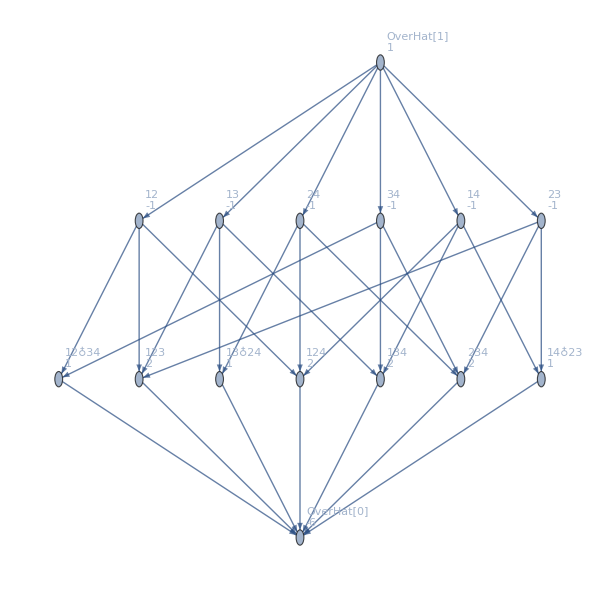

```mathematica
MobiusGraph5[allKey,allGraphs]
```

```mathematica
ExpressionToTable2[reduced]
```

f12==-1+n12
f123==2-n12+n123-n13-n23
f124==2-n12+n124-n14-n24
f13==-1+n13
f134==2-n13+n134-n14-n34
f14==-1+n14
f23==-1+n23
f234==2-n23+n234-n24-n34
f24==-1+n24
f34==-1+n34
f12♁34==1-n12-n34+n12♁34
f13♁24==1-n13-n24+n13♁24
f14♁23==1-n14-n23+n14♁23
fOverHat[0]==-6+2 n12-n123-n124+2 n13-n134+2 n14+2 n23-n234+2 n24+2 n34-n12♁34-n13♁24-n14♁23+nOverHat[0]
fOverHat[1]==1
nOverHat[1]==1

```mathematica
res={ToRules[Reduce[Reduce[zeta.nullVec==fullVec2]&&Fold[And,Table[0≤v≤1,{v,fullVars}]],Join[fullVars,nullVars],Integers]]};TableForm[res]
```

$Aborted

```mathematica
2^vectorLength-1
```

31

```mathematica
With[{exp=Reduce[zeta.NullVector[K4Key]==fullVec2,fullVars,Integers,Backsubstitution->True]},Table[exp[[k,2]],{k,2,vectorLength+1}]]
```

Part::partw: Part 6 of f==0&&f==0&&f==0&&f==0&&f==0 does not exist.

{0,0,0,0,(fOverHat[1]==0&&f23==0&&f12==0&&f13==0&&fOverHat[0]==0)⟦6,2⟧}

```mathematica
en=DeleteDuplicates[Monitor[Table[With[{fullVec3=PadLeft[IntegerDigits[k,2],vectorLength]},
With[{exp=Reduce[zeta.nullVec==fullVec3,nullVars,Integers]},Table[exp[[k,2]],{k,2,vectorLength+1}]]
],{k,0,2^vectorLength-1}],k]];
```

Part::partw: Part 6 of n==0&&n==0&&n==0&&n==0&&n==0 does not exist.

Part::partw: Part 6 of n==2&&n==-1&&n==-1&&n==-1&&n==1 does not exist.

Part::partw: Part 6 of n==-1&&n==0&&n==0&&n==1&&n==0 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
en//Sort//MatrixForm
```

(-1 | -1 | -1 | 1 | (nOverHat[1]==2&&n23==-1&&n12==-1&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
-1 | -1 | -1 | 1 | (nOverHat[1]==3&&n23==-1&&n12==-1&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
-1 | -1 | 0 | 1 | (nOverHat[1]==1&&n23==-1&&n12==-1&&n13==0&&nOverHat[0]==1)⟦6,2⟧
-1 | -1 | 0 | 1 | (nOverHat[1]==2&&n23==-1&&n12==-1&&n13==0&&nOverHat[0]==1)⟦6,2⟧
-1 | 0 | -1 | 1 | (nOverHat[1]==1&&n23==-1&&n12==0&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
-1 | 0 | -1 | 1 | (nOverHat[1]==2&&n23==-1&&n12==0&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
-1 | 0 | 0 | 1 | (nOverHat[1]==0&&n23==-1&&n12==0&&n13==0&&nOverHat[0]==1)⟦6,2⟧
-1 | 0 | 0 | 1 | (nOverHat[1]==1&&n23==-1&&n12==0&&n13==0&&nOverHat[0]==1)⟦6,2⟧
0 | -1 | -1 | 1 | (nOverHat[1]==1&&n23==0&&n12==-1&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
0 | -1 | -1 | 1 | (nOverHat[1]==2&&n23==0&&n12==-1&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
0 | -1 | 0 | 1 | (nOverHat[1]==0&&n23==0&&n12==-1&&n13==0&&nOverHat[0]==1)⟦6,2⟧
0 | -1 | 0 | 1 | (nOverHat[1]==1&&n23==0&&n12==-1&&n13==0&&nOverHat[0]==1)⟦6,2⟧
0 | 0 | -1 | 1 | (nOverHat[1]==0&&n23==0&&n12==0&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
0 | 0 | -1 | 1 | (nOverHat[1]==1&&n23==0&&n12==0&&n13==-1&&nOverHat[0]==1)⟦6,2⟧
0 | 0 | 0 | 0 | (nOverHat[1]==0&&n23==0&&n12==0&&n13==0&&nOverHat[0]==0)⟦6,2⟧
0 | 0 | 0 | 0 | (nOverHat[1]==1&&n23==0&&n12==0&&n13==0&&nOverHat[0]==0)⟦6,2⟧
0 | 0 | 0 | 1 | (nOverHat[1]==-1&&n23==0&&n12==0&&n13==0&&nOverHat[0]==1)⟦6,2⟧
0 | 0 | 0 | 1 | (nOverHat[1]==0&&n23==0&&n12==0&&n13==0&&nOverHat[0]==1)⟦6,2⟧
0 | 0 | 1 | 0 | (nOverHat[1]==-1&&n23==0&&n12==0&&n13==1&&nOverHat[0]==0)⟦6,2⟧
0 | 0 | 1 | 0 | (nOverHat[1]==0&&n23==0&&n12==0&&n13==1&&nOverHat[0]==0)⟦6,2⟧
0 | 1 | 0 | 0 | (nOverHat[1]==-1&&n23==0&&n12==1&&n13==0&&nOverHat[0]==0)⟦6,2⟧
0 | 1 | 0 | 0 | (nOverHat[1]==0&&n23==0&&n12==1&&n13==0&&nOverHat[0]==0)⟦6,2⟧
0 | 1 | 1 | 0 | (nOverHat[1]==-2&&n23==0&&n12==1&&n13==1&&nOverHat[0]==0)⟦6,2⟧
0 | 1 | 1 | 0 | (nOverHat[1]==-1&&n23==0&&n12==1&&n13==1&&nOverHat[0]==0)⟦6,2⟧
1 | 0 | 0 | 0 | (nOverHat[1]==-1&&n23==1&&n12==0&&n13==0&&nOverHat[0]==0)⟦6,2⟧
1 | 0 | 0 | 0 | (nOverHat[1]==0&&n23==1&&n12==0&&n13==0&&nOverHat[0]==0)⟦6,2⟧
1 | 0 | 1 | 0 | (nOverHat[1]==-2&&n23==1&&n12==0&&n13==1&&nOverHat[0]==0)⟦6,2⟧
1 | 0 | 1 | 0 | (nOverHat[1]==-1&&n23==1&&n12==0&&n13==1&&nOverHat[0]==0)⟦6,2⟧
1 | 1 | 0 | 0 | (nOverHat[1]==-2&&n23==1&&n12==1&&n13==0&&nOverHat[0]==0)⟦6,2⟧
1 | 1 | 0 | 0 | (nOverHat[1]==-1&&n23==1&&n12==1&&n13==0&&nOverHat[0]==0)⟦6,2⟧
1 | 1 | 1 | 0 | (nOverHat[1]==-3&&n23==1&&n12==1&&n13==1&&nOverHat[0]==0)⟦6,2⟧
1 | 1 | 1 | 0 | (nOverHat[1]==-2&&n23==1&&n12==1&&n13==1&&nOverHat[0]==0)⟦6,2⟧)

```mathematica
Length[en]
```

32

```mathematica
Length[Keys[allGraphs]]
```

15

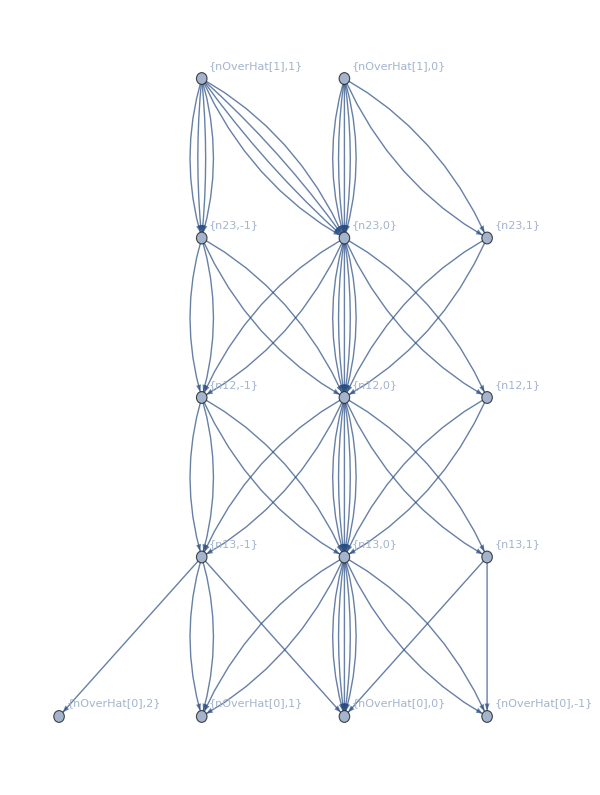

```mathematica
Graph[Flatten[Table[With[{v=NullVector[k]},Table[DirectedEdge[{nullVars[[k1]],Style[v[[k1]],Red]},{nullVars[[k1+1]],Style[v[[k1+1]],Red]}],{k1,vectorLength-1}]],{k,Keys[allGraphs]}]],VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->False,ImageSize->600]
```

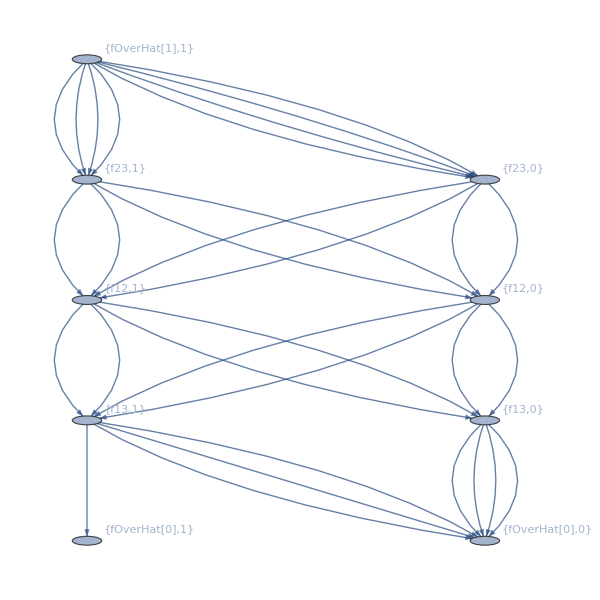

```mathematica
Graph[Flatten[Table[With[{v=FullVector[k]},Table[DirectedEdge[{fullVars[[k1]],v[[k1]]},{fullVars[[k1+1]],v[[k1+1]]}],{k1,vectorLength-1}]],{k,
Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==nodeCount&]}]],VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->False, ImageSize->{600,600}]
```